```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]]β1]Exp[x2[[k]]β2]Exp[x3[[k]]β3])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]]β1]Exp[x2[[k]]β2]Exp[x3[[k]]β3]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
Cov2={4,20,1,1,32,32,24,24,24,30,0,8,8,12,20,32,24};
Cov3={1,0,0.5,0.5,2,5,4.5,2.5,4,2,0,4,6,4,6,10,8};
```

```mathematica
(* Loop to generate failure counts *)
ω=55;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]],Cov2[[j]],Cov3[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->3,β->{0.21774224,0.03132722,0.17702043},h->GM/.{b->0.026192}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{5,1,1,2,1,2,3,3,0,1,1,1,1,1,0,0,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{5,6,7,9,10,12,15,18,18,19,20,21,22,23,23,23,23}

```mathematica
(* MLEs *)
h=GM;
lnLa=lnL/.{y-> FC,x1->Cov1,x2->Cov2,x3->Cov3};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,β2]},{0==D[lnLa,β3]},{0==D[lnLa,b]}},{{ω,55},{β1,0.217},{β2,0.0313},{β3,0.177},{b,0.0261}},MaxIterations->100000]
```

{ω→23.0039,β1→0.356822,β2→-0.0528748,β3→0.233331,b→0.137922}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]]β1]Exp[x2[[g]]β2]Exp[x3[[g]]β3])/.Rules/.{x1->Cov1,x2->Cov2,x3->Cov3};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
];
HωList//N
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{3.29488,4.30661,7.18796,9.56446,10.3888,12.2956,15.4034,18.1109,18.6783,19.6659,20.2835,21.2205,22.2064,22.4173,22.5783,22.7745,23.}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 5
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 5
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

47.2739

51.4399

8.1859

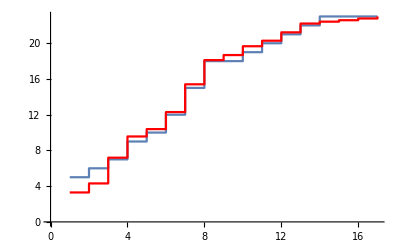

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red,Joined->True,InterpolationOrder->0];
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Intervals=Table[i,{i,1,17}];
If[AIC<65&&BIC<65&&SSE<35,Export["GM_3cov_sim.xlsx",Transpose[{Intervals,FC,Cov1,Cov2,Cov3}]]]
```

GM_3cov_sim.xlsx